# Approximating Poisson Distribution: An Monte Carlo Approach

## Abstract

In this notebook, we illustrate how to construct an approximate distribution of Poisson Distribution, we mainly use the Monte Carlo method, we will demonstrate that after many many times of experiments, using the sample data collected from the experiments, we can derive a pretty good approximation of Poisson Distribution which has only a subtle differences in C.D.F. and P.D.F. when the amount of trials is large enough.

## Poisson Distribution

A Poisson Distribution describes the distribution of the amount of happens of a specific event within a period, e.g., how many cars just passed a road in 1 hour, how many customers just enter a bank in 30 minutes, how many particles will burst out a radiative source in a period, let’s say Xcars will pass that road in 1 hour, then, the random variable X obeys a Poisson Distribution, denoted as

X \[Distributed] PoissonDistribution[λ]

where λ is the hourly average traffic of that road, then given an non-negative integer x, we can compute the probability of “4 cars pass that road in 1 hour”, which is

Pr(X=4)=(λ^k e^-λ)/(k!)=(10^4 e^-10)/4!

let’s say, in average, there has 10 cars pass that road, that is λ=10, so that the probability of “4 cars pass that road in 1 hour” is (10^4 e^-10)/4!. Now hopefully you see the basics of Poisson Distribution.

## How to Approximate a Poisson Distribution

Let’s say that We don’t know the exact expression of the cumulative distribution function of Poisson Distribution, and We only know that there’s a random variable X which obeys a Poison Distribution of some parameter λ, i.e. X \[Distributed] PoissonDistribution[λ], given only this, how can we compute the probability Pr(X≤x), where  x is a non negative integer ?

Shall notice that there is a basic assumption when We say some random variable X obeys a Poisson Distribution, it is usually assumed that in every interval, the mean amount of happens of that specific event does not change, simply speaking, let’s take the car-pass-road case for example, we assumed that no matter which hour in a day is, the expectation of the amount of times the car pass that road in that hour are unique, say that λ, the parameter of Poisson Distribution, is λ=4, which equivalently means, that, the average traffic in 0 am is 4, and the average traffic in 1 am is 4, and the average traffic in 2,3,4,5, until 22, 23 hour of that day is 4, no matter which hour it is. This is what that basic assumption means. Hopefully you understand.

So, it that basic assumption useful? Yes it is useful. In Monte Carlo way, let’s say that there are n intervals in total, that is, whole time range can be split into to n parts, and in each interval, the event are “expected” to happen λ times, which is the parameter of a Poisson Distribution, also the “mean traffic” in the car-pass-road case as we denoted, so after all n intervals gone, the event are “expected to” happened nλ times altogether. Then, in Monte Carlo’s point of view, each happening of the event (there are nλ happenings altogether) can randomly “choose” which interval it “wanted to” happen at, let’s take an example, say there is a array of event, which’s length is nλ

events[] = [event[1], event[2], ..., event[n λ]]

Then, for each event in the array events[], say, firstly, it is event[1], then event[1] will randomly choose a interval, in

intervals[] = [interval[1], interval[2], ..., interval[n]]

say that event[1] just randomly picked interval[4], then event[2] randomly picked interval[7], then event[3] randomly picked interval[2], and so on until all event in events[] picked their own interval[i] to happen, then, for each interval in intervals[], we can counts that how many event[i]s just fallen into it, for example, event[2], event[4], event[7], event[11] all take interval[6], then, it will means that there are 4 event[i]s fallen into interval[6], we can count that, it is easy. Same operation perform on every interval, we can have such an table which maps interval[i] to the amount of event[i]s fallen to it, it may seems like below

counts = <| interval[1] -> 7, interval[2] -> 2, interval[3] -> 11, ... |>

then We only take the values from the table, we got

data = [7, 2, 11, ...]

then you will understand that this array, this array named data, shall distributed like Poisson Distribution.

## Compute

First we cut the whole time range into n=8000000 parts, the larger n is, the more accurate the result will be.

```mathematica
n=8000000
```

8000000

Just assign a concrete value to symbol λ, which is λ=4, so that we can compute the numerical value, and will be easier to compare and plot. So, you can say that, We are gonna to approximate PoissonDistribution[λ=4].

```mathematica
lambda=4
```

4

Then We generate nλ random integers that evenly distributed across 1 to n, which correspond to interval[1] to interval[n] like we just said in previous section.

```mathematica
sampleData=Ceiling[RandomVariate[UniformDistribution[{0,n}],n*lambda]];
```

Counts “how many events caught” for each interval[i].

```mathematica
sampleDataCounts=Counts[sampleData];
```

Extract the values part.

```mathematica
stats=Values[sampleDataCounts];
```

Construct the empirical distribution using data we just collected, the array named stats.

```mathematica
empiricalDistribution=EmpiricalDistribution[stats]
```

DataDistribution[…]

Try some value, to see the Pr(X≤x) computed from the empirical distribution.

```mathematica
N[PDF[empiricalDistribution,{0,1,2,3,4,5,6,7}]]
```

{0.,0.0745656,0.148999,0.199489,0.199073,0.159294,0.105902,0.0606136}

Try some value, to see the Pr(X≤x) computed PoissonDistribution[λ], which is, of course, theoretical.

```mathematica
N[PDF[PoissonDistribution[lambda],{0,1,2,3,4,5,6,7}]]
```

{0.0183156,0.0732626,0.146525,0.195367,0.195367,0.156293,0.104196,0.0595404}

Compare the plot of the empirical P.D.F. and the theoretical P.D.F..

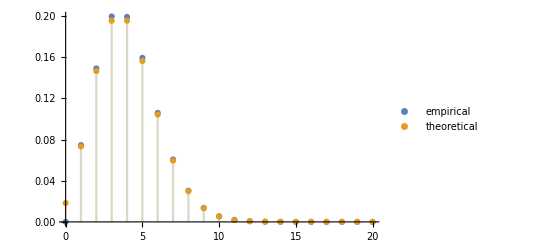

```mathematica
DiscretePlot[{PDF[empiricalDistribution,x],PDF[PoissonDistribution[lambda],x]},{x,0,20},PlotLegends->{"empirical","theoretical"}]
```

Compare the plot of the empirical C.D.F. and the theoretical C.D.F..

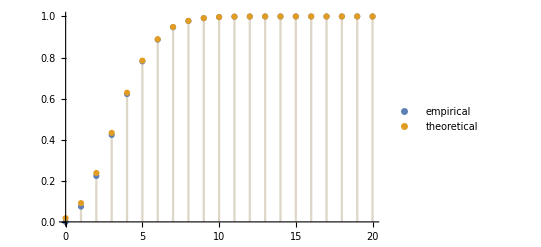

```mathematica
DiscretePlot[{CDF[empiricalDistribution,x],CDF[PoissonDistribution[lambda],x]},{x,0,20},PlotLegends->{"empirical","theoretical"}]
```

We can find that, there only subtle differences in C.D.F. or P.D.F., because n is so large, the empirical distribution and theoretical (which is accurate) PoissonDistribution are nearly fitted into one.